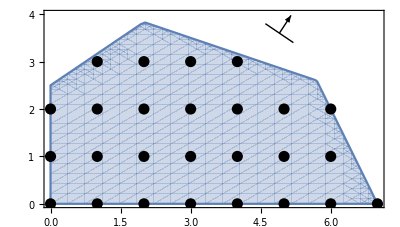

F:\Univ\_PhD\TA\MATH0462\Syllabus\3_BB_graphical_0.png

```mathematica
p=Show[{
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14,{x,0,7},{y,0,4},
Epilog->{
(* Feasible points. *)
PointSize[.02],
Point[{
{0,0},{0,1},{0,2},
{1,0},{1,1},{1,2},{1,3},
{2,0},{2,1},{2,2},{2,3},
{3,0},{3,1},{3,2},{3,3},
{4,0},{4,1},{4,2},{4,3},
{5,0},{5,1},{5,2},
{6,0},{6,1},{6,2},
{7,0}
}],
(* Objective. *)
Arrow[{{49/10,18/5},{49/10,18/5}+{2,3}/8}],
Line[{{49/10,18/5}-{-3,2}/10,{49/10,18/5}+{-3,2}/10}]
},
AspectRatio->4/7]
}]
Export[NotebookDirectory[]<>"3_BB_graphical_0.png",p]
```

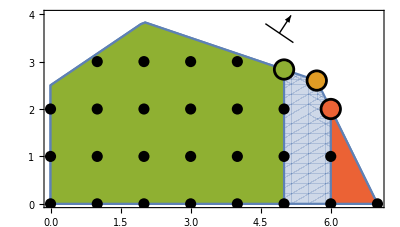

F:\Univ\_PhD\TA\MATH0462\Syllabus\3_BB_graphical_1.png

```mathematica
p=Show[{
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14,{x,0,7},{y,0,4},
Epilog->{
(* Feasible points. *)
PointSize[.02],
Point[{
{0,0},{0,1},{0,2},
{1,0},{1,1},{1,2},{1,3},
{2,0},{2,1},{2,2},{2,3},
{3,0},{3,1},{3,2},{3,3},
{4,0},{4,1},{4,2},{4,3},
{5,0},{5,1},{5,2},
{6,0},{6,1},{6,2},
{7,0}
}],
(* Objective. *)
Arrow[{{49/10,18/5},{49/10,18/5}+{2,3}/8}],
Line[{{49/10,18/5}-{-3,2}/10,{49/10,18/5}+{-3,2}/10}],
(* Optimal points. *)
PointSize[.04],Black,Point[{{57/10,13/5},{5,17/6},{6,2}}],
PointSize[.03],
ColorData[97,2],Point[{57/10,13/5}],
ColorData[97,3],Point[{5,17/6}],
ColorData[97,4],Point[{6,2}]
},
AspectRatio->4/7],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5,{x,0,7},{y,0,4},PlotStyle->ColorData[97,3]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≥6,{x,0,7},{y,0,4},PlotStyle->ColorData[97,4]]
}]
Export[NotebookDirectory[]<>"3_BB_graphical_1.png",p]
```

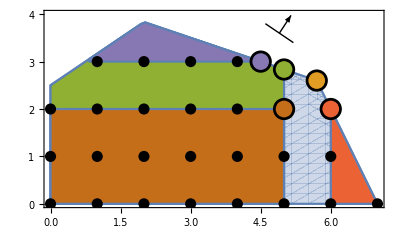

F:\Univ\_PhD\TA\MATH0462\Syllabus\3_BB_graphical_2.png

```mathematica
p=Show[{
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14,{x,0,7},{y,0,4},
Epilog->{
(* Feasible points. *)
PointSize[.02],
Point[{
{0,0},{0,1},{0,2},
{1,0},{1,1},{1,2},{1,3},
{2,0},{2,1},{2,2},{2,3},
{3,0},{3,1},{3,2},{3,3},
{4,0},{4,1},{4,2},{4,3},
{5,0},{5,1},{5,2},
{6,0},{6,1},{6,2},
{7,0}
}],
(* Objective. *)
Arrow[{{49/10,18/5},{49/10,18/5}+{2,3}/8}],
Line[{{49/10,18/5}-{-3,2}/10,{49/10,18/5}+{-3,2}/10}],
(* Optimal points. *)
PointSize[.04],Black,Point[{{57/10,13/5},{5,17/6},{6,2},{9/2,3},{5,2}}],
PointSize[.03],
ColorData[97,2],Point[{57/10,13/5}],
ColorData[97,3],Point[{5,17/6}],
ColorData[97,4],Point[{6,2}],
ColorData[97,5],Point[{9/2,3}],
ColorData[97,6],Point[{5,2}]
},
AspectRatio->4/7],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5,{x,0,7},{y,0,4},PlotStyle->ColorData[97,3]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≥6,{x,0,7},{y,0,4},PlotStyle->ColorData[97,4]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5&&y≥3,{x,0,7},{y,0,4},PlotStyle->ColorData[97,5]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5&&y≤2,{x,0,7},{y,0,4},PlotStyle->ColorData[97,6]]
}]
Export[NotebookDirectory[]<>"3_BB_graphical_2.png",p]
```

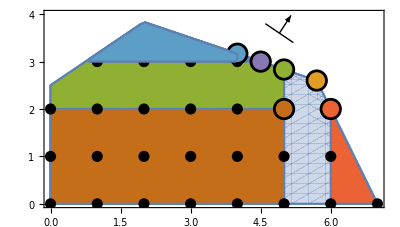

F:\Univ\_PhD\TA\MATH0462\Syllabus\3_BB_graphical_3.png

```mathematica
p=Show[{
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14,{x,0,7},{y,0,4},
Epilog->{
(* Feasible points. *)
PointSize[.02],
Point[{
{0,0},{0,1},{0,2},
{1,0},{1,1},{1,2},{1,3},
{2,0},{2,1},{2,2},{2,3},
{3,0},{3,1},{3,2},{3,3},
{4,0},{4,1},{4,2},{4,3},
{5,0},{5,1},{5,2},
{6,0},{6,1},{6,2},
{7,0}
}],
(* Objective. *)
Arrow[{{49/10,18/5},{49/10,18/5}+{2,3}/8}],
Line[{{49/10,18/5}-{-3,2}/10,{49/10,18/5}+{-3,2}/10}],
(* Optimal points. *)
PointSize[.04],Black,Point[{{57/10,13/5},{5,17/6},{6,2},{9/2,3},{5,2},{4,19/6}}],
PointSize[.03],
ColorData[97,2],Point[{57/10,13/5}],
ColorData[97,3],Point[{5,17/6}],
ColorData[97,4],Point[{6,2}],
ColorData[97,5],Point[{9/2,3}],
ColorData[97,6],Point[{5,2}],
ColorData[97,7],Point[{4,19/6}]
},
AspectRatio->4/7],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5,{x,0,7},{y,0,4},PlotStyle->ColorData[97,3]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≥6,{x,0,7},{y,0,4},PlotStyle->ColorData[97,4]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5&&y≥3,{x,0,7},{y,0,4},PlotStyle->ColorData[97,5]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5&&y≤2,{x,0,7},{y,0,4},PlotStyle->ColorData[97,6]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤4&&y≥3,{x,0,7},{y,0,4},PlotStyle->ColorData[97,7]]
}]
Export[NotebookDirectory[]<>"3_BB_graphical_3.png",p]
```

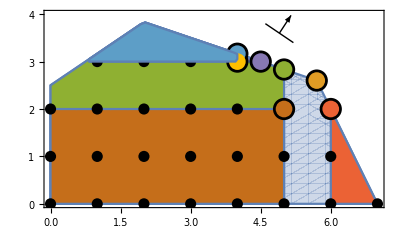

F:\Univ\_PhD\TA\MATH0462\Syllabus\3_BB_graphical_4.png

```mathematica
p=Show[{
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14,{x,0,7},{y,0,4},
Epilog->{
(* Feasible points. *)
PointSize[.02],
Point[{
{0,0},{0,1},{0,2},
{1,0},{1,1},{1,2},{1,3},
{2,0},{2,1},{2,2},{2,3},
{3,0},{3,1},{3,2},{3,3},
{4,0},{4,1},{4,2},{4,3},
{5,0},{5,1},{5,2},
{6,0},{6,1},{6,2},
{7,0}
}],
(* Objective. *)
Arrow[{{49/10,18/5},{49/10,18/5}+{2,3}/8}],
Line[{{49/10,18/5}-{-3,2}/10,{49/10,18/5}+{-3,2}/10}],
(* Optimal points. *)
PointSize[.04],Black,Point[{{57/10,13/5},{5,17/6},{6,2},{9/2,3},{5,2},{4,19/6},{4,3}}],
PointSize[.03],
ColorData[97,2],Point[{57/10,13/5}],
ColorData[97,3],Point[{5,17/6}],
ColorData[97,4],Point[{6,2}],
ColorData[97,5],Point[{9/2,3}],
ColorData[97,6],Point[{5,2}],
ColorData[97,7],Point[{4,19/6}],
ColorData[97,8],Point[{4,3}]
},
AspectRatio->4/7],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5,{x,0,7},{y,0,4},PlotStyle->ColorData[97,3]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≥6,{x,0,7},{y,0,4},PlotStyle->ColorData[97,4]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5&&y≥3,{x,0,7},{y,0,4},PlotStyle->ColorData[97,5]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤5&&y≤2,{x,0,7},{y,0,4},PlotStyle->ColorData[97,6]],
RegionPlot[-2/3 x+y≤5/2&&1/3 x+y≤9/2&&2x+y≤14&&x≤4&&y≥3,{x,0,7},{y,0,4},PlotStyle->ColorData[97,7]]
}]
Export[NotebookDirectory[]<>"3_BB_graphical_4.png",p]
```

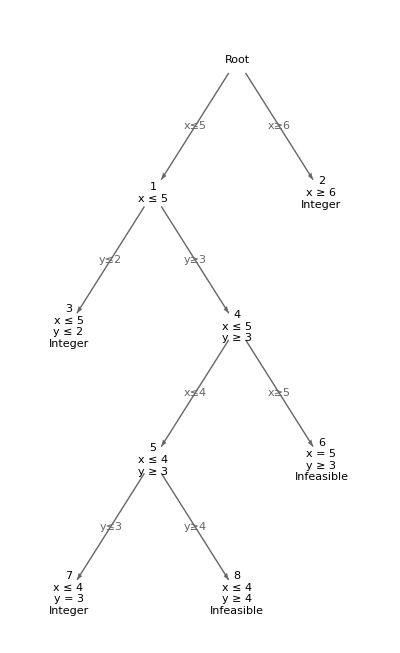

F:\Univ\_PhD\TA\MATH0462\Syllabus\3_BB_graphical_tree.png

```mathematica
p=With[{root="Root",n1="1\nx ≤ 5",n2="2\nx ≥ 6\nInteger",n3="3\nx ≤ 5\ny ≤ 2\nInteger",n4="4\nx ≤ 5\ny ≥ 3",n5="5\nx ≤ 4\ny ≥ 3",n6="6\nx = 5\ny ≥ 3\nInfeasible",n7="7\nx ≤ 4\ny = 3\nInteger",n8="8\nx ≤ 4\ny ≥ 4\nInfeasible"},
TreePlot[
{
{root->n1,x≤5},{root->n2,x≥6},
{n1->n3,y≤2},{n1->n4,y≥3},
{n4->n5,x≤4},{n4->n6,x≥5},
{n5->n7,y≤3},{n5->n8,y≥4}
},Automatic,root,
VertexLabeling->True,
EdgeRenderingFunction->({GrayLevel[0.4],
Arrow[#1,0.1],
Text[#3,(* #2: 0->1; #3: label *)
{.5*#1[[1]][[1]]+.5*#1[[2]][[1]],.5*#1[[1]][[2]]+.5*#1[[2]][[2]]},
Background->White]}&)
]
]
Export[NotebookDirectory[]<>"3_BB_graphical_tree.png",p]
```